## Lecture examples

```mathematica
PDF[DiscreteUniformDistribution[{1,6}],x]
```

Piecewise[{{1/6, 1≤x≤6}, {0, True}}]

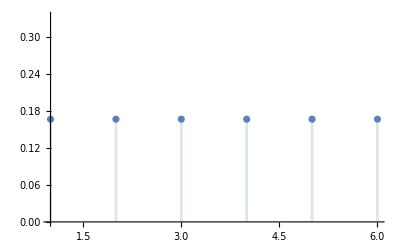

```mathematica
DiscretePlot[PDF[DiscreteUniformDistribution[{1,6}],x], {x,1,6}]
```

```mathematica
𝒟=ProductDistribution[{DiscreteUniformDistribution[{1,6}],2}];
```

```mathematica
DiscretePlot3D[PDF[𝒟,{x,y}],{x,0,12},{y,0,12},ExtentSize->Full,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
DiscretePlot[PDF[PoissonDistribution[6],x], {x,0,12}]
```

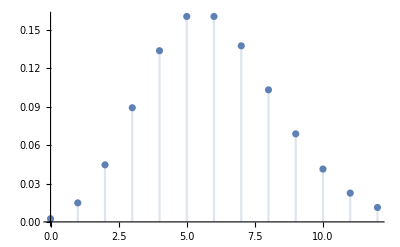

-Graphics-

```mathematica
ℬ=ProductDistribution[{PoissonDistribution[6],2}];
```

```mathematica
DiscretePlot3D[PDF[ℬ,{x,y}],{x,0,12},{y,0,12},ExtentSize->Full,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
𝒢=ProductDistribution[UniformDistribution[{1,6}],PoissonDistribution[6]];
```

```mathematica
Map[DiscretePlot3D[PDF[𝒢,{x,y}],{x,0,12},{y,0,12},ExtentSize->Full,ColorFunction->Function[{x,y,z},#],PlotLabel->#]&,{Hue[x],Hue[y],Hue[z]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
DiscretePlot3D[PDF[𝒢,{x,y}],{x,0,12},{y,0,12},ExtentSize->Full,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Mathematica examples

```mathematica
Map[DiscretePlot3D[PDF[𝒟,{x,y}],{x,0,12},{y,0,12},ExtentSize->Full,ColorFunction->Function[{z},#],PlotLabel->#]&,{Hue[z]}]
```

{-Graphics3D-}

```mathematica
Map[DiscretePlot3D[PDF[MultivariatePoissonDistribution[5,{2,3}],{x,y}],{x,0,15},{y,0,15},Joined->True,PlotRange->All,ColorFunction->Function[{x,y,z},#],PlotLabel->#]&,{Hue[x],Hue[y],Hue[z]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
DiscretePlot3D[PDF[MultivariatePoissonDistribution[1,{1,1}],{x,y}],{x,0,15},{y,0,15},ExtentSize->Full,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Multivariate Normal Distribution

```mathematica
data=RandomVariate[𝒹=MultinormalDistribution[{1,2},{{2,1/2},{1/2,2}}],10^3];
```

```mathematica
{Histogram3D[data,20,"PDF",ColorFunction->"Rainbow",PlotRange->{{-2,4},{-2,4},All}],Plot3D[PDF[𝒹,{x,y}],{x,-2,4},{y,-2,4},ColorFunction->"Rainbow",PlotPoints->35,PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

## Bivariate Normal Distribution

```mathematica
sample=RandomVariate[𝒹=BinormalDistribution[{1,2},{1.5,2},0.6],10^5];
{Histogram3D[sample,30,"PDF",ColorFunction->"Rainbow",PlotRange->{{-5,6},{-3,7},All}],Plot3D[PDF[𝒹,{x,y}],{x,-5,6},{y,-3,7},ColorFunction->"Rainbow",PlotPoints->35,PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Histogram3D[sample,30,"PDF",ColorFunction->"Rainbow",PlotRange->{{-5,6},{-3,7},All}]
```

-Graphics3D-

```mathematica
Plot3D[PDF[𝒹,{x,y}],{x,-5,6},{y,-3,7},ColorFunction->"Rainbow",PlotPoints->35,PlotRange->All]
```

-Graphics3D-

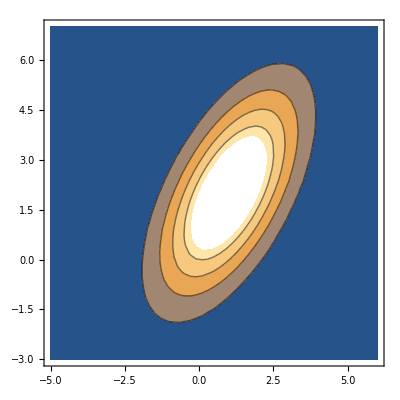

```mathematica
ContourPlot[PDF[𝒹,{x,y}],{x,-5,6},{y,-3,7}]
```